```mathematica
NotebookEvaluate["definitions.nb"]
```

This code has been superseded by more efficient, cluster code to compute these quantities: see https://github.com/CKQu1/extended-criticality-dnn/tree/master/random_dnn

## Column-structured heavy-tailed random matrix theory

```mathematica
SDist[α_]:=With[{C=Function[α1,Gamma[1+α1]Sin[π α1/2]/π]},StableDistribution[α/2,1,0,(C[α]/(4C[α/2]))^(2/α)]]
```

z, χFn assumed to be real in these inputs for speed

Compute the density of states over a vector of eigenvalues, with the spectral radius automatically determined to within δr:

```mathematica
DOSVector[α_?NumericQ,yFrac_?NumericQ,χDist_,χFn_,nSamples_:100000,δr_:.01]:=With[{SDistSamples=RandomVariate[SDist[α],nSamples],y0=((4 Cos[(π α)/4] Csc[(π α)/2] Sin[(π α)/4])/Gamma[1+α])^(1/α)},With[{samples={SDistSamples,RandomSample@SDistSamples,χFn@RandomVariate[χDist,nSamples]}},Table[r~List~With[{y=Abs[y]/.FindRoot[1-Mean[((#3^2#1)/(r^2+#3^2y^2#1 #2))^(α/2)&~MapThread~samples],{y,1,0.5}]},With[{δy=-Mean[((#3^2#1)^(α/2))/((r^2+#3^2y^2#1 #2)^(α/2+1))&~MapThread~samples]/Mean[((#3^2#1)/(r^2+#3^2y^2#1 #2))^(α/2+1)2y#2&~MapThread~samples]},(y^2-2 r^2 y δy)/π Mean[(#3^2#1#2)/((r^2+#3^2y^2#1 #2)^2)&~MapThread~samples]]],{r,Range[δr,Abs@z/.FindRoot[1-Mean[((#3^2#1)/(z^2+#3^2(yFrac y0)^2#1 #2))^(α/2)&~MapThread~samples],{z,1,2}],δr]}]]]
```

The following function is useful when computing only a single parameter set -- parallelising over alpha and g using the above function is faster than parallelising over r = Abs[eigenvalue] using this function:

```mathematica
DOSVectorParallel[α_?NumericQ,yFrac_?NumericQ,χDist_,χFn_,nSamples_:100000,δr_:.01]:=(ResourceFunction["ParallelMapMonitored"];ResourceFunction["ParallelMapMonitored"][r↦r~List~Quiet@With[{SDistSamples=RandomVariate[SDist[α],nSamples]},With[{samples={SDistSamples,RandomSample@SDistSamples,χFn@RandomVariate[χDist,nSamples]}},With[{y=Abs[y]/.FindRoot[1-Mean[((#3^2#1)/(r^2+#3^2y^2#1 #2))^(α/2)&~MapThread~samples],{y,1,0.5}]},With[{δy=-Mean[((#3^2#1)^(α/2))/((r^2+#3^2y^2#1 #2)^(α/2+1))&~MapThread~samples]/Mean[((#3^2#1)/(r^2+#3^2y^2#1 #2))^(α/2+1)2y#2&~MapThread~samples]},(y^2-2 r^2 y δy)/π Mean[(#3^2#1#2)/((r^2+#3^2y^2#1 #2)^2)&~MapThread~samples]]]]],With[{samples={RandomVariate[SDist[α],nSamples],RandomVariate[SDist[α],nSamples],χFn@RandomVariate[χDist,nSamples]},y0=((4 Cos[(π α)/4] Csc[(π α)/2] Sin[(π α)/4])/Gamma[1+α])^(1/α)},Range[δr,Abs@z/.Quiet@FindRoot[1-Mean[((#3^2#1)/(z^2+#3^2(yFrac y0)^2#1 #2))^(α/2)&~MapThread~samples],{z,1,2}],δr]]])
```

```mathematica
ClearAll[yStarGaussian];yStarGaussian[z_?NumericQ,χDist_,χFn_]:=With[{α=2,S=1,Sp=1},Abs@yStar/.FindRoot[1-NExpectation[((χFn[χ]^2 S)/(z^2+yStar^2 χFn[χ]^2 S Sp))^(α/2),χ\[Distributed]χDist],{yStar,1,.5}]]
```

```mathematica
ClearAll[DOSGaussian];DOSGaussian[z_?NumericQ,χDist_,χFn_]:=With[{yStar=yStarGaussian[z,χDist,χFn],α=2,S=1,Sp=1},With[{δyStar=-(NExpectation[((χFn[χ]^2 S)^(α/2))/((z^2+yStar^2 χFn[χ]^2 S Sp)^(α/2+1)),χ\[Distributed]χDist]/NExpectation[((χFn[χ]^2 S)^(α/2+1)2yStar Sp)/((z^2+yStar^2 χFn[χ]^2 S Sp)^(α/2+1)),χ\[Distributed]χDist])},(yStar^2-2 z^2 yStar δyStar)/π NExpectation[(χFn[χ]^2 S Sp)/((z^2+yStar^2 χFn[χ]^2 S Sp)^2),χ\[Distributed]χDist]]]
```

The following functions are too slow and are replaced by the fast vectorised versions above:

```mathematica
ClearAll[Radius,RadiusEqnRHS];RadiusEqnRHS[α_?NumericQ,yFrac_?NumericQ,χDist_,χFn_,z_?NumericQ,nReps_:1]:=With[{y0=((4 Cos[(π α)/4] Csc[(π α)/2] Sin[(π α)/4])/Gamma[1+α])^(1/α)},Mean@Table[NExpectation[((χFn[χ]^2 S)/(z^2+(yFrac y0)^2 χFn[χ]^2 S Sp))^(α/2),{S\[Distributed]SDist[α],Sp\[Distributed]SDist[α],χ\[Distributed]χDist},Method->"MonteCarlo"],nReps]];Radius[α_?NumericQ,yFrac_?NumericQ,χDist_,χFn_,nReps_:1]:=Abs@z/.FindRoot[1-RadiusEqnRHS[α,yFrac,χDist,χFn,z,nReps],{z,1,2}]
```

```mathematica
ClearAll[yStar,yStarEqnRHS];yStarEqnRHS[α_?NumericQ,z_?NumericQ,χDist_,χFn_,yStar_?NumericQ,nReps_:1]:=Mean@Table[NExpectation[((χFn[χ]^2 S)/(z^2+yStar^2 χFn[χ]^2 S Sp))^(α/2),{S\[Distributed]SDist[α],Sp\[Distributed]SDist[α],χ\[Distributed]χDist},Method->"MonteCarlo"],nReps];yStar[α_?NumericQ,z_?NumericQ,χDist_,χFn_,nReps_:1]:=With[{y0=((4 Cos[(π α)/4] Csc[(π α)/2] Sin[(π α)/4])/Gamma[1+α])^(1/α)},Abs@yStar/.FindRoot[1-yStarEqnRHS[α,z,χDist,χFn,yStar,nReps],{yStar,.01y0,.01y0,y0}]]
```

```mathematica
ClearAll[DOS];DOS[α_?NumericQ,z_?NumericQ,χDist_,χFn_,nReps_:1]:=With[{yStar=yStar[α,z,χDist,χFn,nReps]},With[{δyStar=-(Mean@Table[NExpectation[((χFn[χ]^2 S)^(α/2))/((z^2+yStar^2 χFn[χ]^2 S Sp)^(α/2+1)),{S\[Distributed]SDist[α],Sp\[Distributed]SDist[α],χ\[Distributed]χDist},Method->"MonteCarlo"],nReps]/Mean@Table[NExpectation[((χFn[χ]^2 S)^(α/2+1)2yStar Sp)/((z^2+yStar^2 χFn[χ]^2 S Sp)^(α/2+1)),{S\[Distributed]SDist[α],Sp\[Distributed]SDist[α],χ\[Distributed]χDist},Method->"MonteCarlo"],nReps])},(yStar^2-2 z^2 yStar δyStar)/π Mean@Table[NExpectation[(χFn[χ]^2 S Sp)/((z^2+yStar^2 χFn[χ]^2 S Sp)^2),{S\[Distributed]SDist[α],Sp\[Distributed]SDist[α],χ\[Distributed]χDist},Method->"MonteCarlo"],nReps]]]
```

## Jacobian functions

These functions compute the stationary distribution of network activity to construct the Jacobian parameters, then run the column-structured RMT functions. The commented-out expressions have been replaced with fast variants which reuse samples when possible, while maintaining acceptable performance.

JacobianOrderedTransition: Find the gain g such that the p-characteristic spectral radius of the shifted Jacobian is 1 (this function is self-contained):

```mathematica
ClearAll[JacobianOrderedTransition,JacobianOrderedTransitionEqnRHS];JacobianOrderedTransitionEqnRHS[α_?NumericQ,yFrac_?NumericQ,ϕ_,g_?NumericQ,nReps_:1]:=With[{y0=((4 Cos[(π α)/4] Csc[(π α)/2] Sin[(π α)/4])/Gamma[1+α])^(1/α),χFn=g ϕ'[#]&,χDist=StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)/.(*FindRoot[Abs[s]-NExpectation[Abs[ϕ[h]]^α,h\[Distributed]StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)]],{s,1,.5}]*)With[{samples=RandomVariate[StableDistribution[α,0,0,(1/2)^(1/α)],10000]},FindRoot[Abs[s]-Mean[Abs[ϕ[g Abs[s]^(1/α)#]]^α&~Map~samples],{s,1,.5}]]]},Mean@Table[NExpectation[((χFn[χ]^2 S)/(1+(yFrac y0)^2 χFn[χ]^2 S Sp))^(α/2),{S\[Distributed]SDist[α],Sp\[Distributed]SDist[α],χ\[Distributed]χDist},Method->"MonteCarlo"],nReps](*This has poor accuracy: With[{nSamples=100000},With[{samples={RandomVariate[SDist[α],nSamples],RandomVariate[SDist[α],nSamples],χFn@RandomVariate[χDist,nSamples]}},Mean[((#3^2#1)/(1+#3^2(yFrac y0)^2#1 #2))^(α/2)&~MapThread~samples]]]*)];JacobianOrderedTransition[α_?NumericQ,yFrac_?NumericQ,ϕ_,nReps_:1]:=Abs@g/.FindRoot[1-JacobianOrderedTransitionEqnRHS[α,yFrac,ϕ,Abs@g,nReps],{g,1,.5}]
```

```mathematica
ClearAll[JacobianDOSVector];JacobianDOSVector[α_?NumericQ,g_?NumericQ,yFrac_?NumericQ,ϕ_,nSamples_:100000,parallel_:False]:=With[{χFn=g ϕ'[#]&,χDist=StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)/.FindRoot[Abs[s]-NExpectation[Abs[ϕ[h]]^α,h\[Distributed]StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)]],{s,1,.5}]]},If[parallel,DOSVectorParallel,DOSVector][α,yFrac,χDist,χFn,nSamples]];
```

```mathematica
ClearAll[JacobianDOSGaussianVector];JacobianDOSGaussianVector[g_?NumericQ,ϕ_]:=With[{α=2},With[{χFn=g ϕ'[#]&,χDist=StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)/.FindRoot[Abs[s]-NExpectation[Abs[ϕ[h]]^α,h\[Distributed]StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)]],{s,1,.5}]]},ParallelTable[{z,DOSGaussian[z,χDist,χFn]},{z,0.01,NExpectation[χFn[χ]^2,χ\[Distributed]χDist]^(1/2),.01}]]];
```

```mathematica
ClearAll[JacobianGaussianRadius];JacobianGaussianRadius[g_?NumericQ,ϕ_]:=With[{α=2},With[{χFn=g ϕ'[#]&,χDist=StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)/.FindRoot[Abs[s]-NExpectation[Abs[ϕ[h]]^α,h\[Distributed]StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)]],{s,1,.5}]]},NExpectation[χFn[χ]^2,χ\[Distributed]χDist]^(1/2)]]
```

Randomly sample Jacobian matrices:

```mathematica
ClearAll[JacobianMatrix];JacobianMatrix[α_?NumericQ,g_?NumericQ,ϕ_,n_]:=With[{χFn=g ϕ'[#]&,χDist=StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)/.FindRoot[Abs[s]-NExpectation[Abs[ϕ[h]]^α,h\[Distributed]StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)]],{s,1,.5}]]},RandomVariate[StableDistribution[α,0,0,(2n)^(-1/α)],{n,n}].DiagonalMatrix[χFn@RandomVariate[χDist,n]]];
```

## Jacobian spectra plots

```mathematica
With[{α=1.2,g=1.75},Quiet@JacobianDOSVector[α,g,.01,Tanh,100000,True]]//BinarySerialize
```

ByteArray[…]

```mathematica
With[{α=1.2,g=1.75},Quiet@Eigenvalues@JacobianMatrix[α,g,Tanh,2000]]//BinarySerialize
```

ByteArray[…]

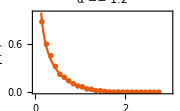

```mathematica
With[{xLim=3,yLim=1,ticksSize=Medium,plotStyle=ColorData[108],label={ShiftFrameLabel[15]@"|z|",ShiftFrameLabel[-5]@"ρ(z)"},eigs=BinaryDeserialize@ResourceFunction["EvaluatePreviousCell"][],DOSvector=BinaryDeserialize@ResourceFunction["EvaluatePreviousCell"][3]},Show[DOSvector//ListLinePlot[#,PlotRange->{{0,xLim},{0,yLim}},ImageSize->Small,Frame->{True,True,False,False},FrameLabel->label,PlotLabel->StringTemplate["α == ``"]@1.2,Evaluate@FigureStyle@pubStyle[ticksSize],LabelStyle->pubStyle[],PlotStyle->plotStyle,ImagePadding->{{50,10},{50,10}}]&,{#1,#2/(2π#1)}&@@@(HistogramPDFList[#,{.1}]&)@Abs@eigs//ListPlot[#,PlotRange->{{0,xLim},{0,yLim}},PlotMarkers->{"OpenMarkers",Small},PlotStyle->plotStyle]/.{p:_Disk|_Polygon:>{FaceForm[],p}}&,Graphics@Inset[Show[ListPlot[ReIm@eigs,PlotRange->{{-xLim,xLim},{-xLim,xLim}},PlotMarkers->{"OpenMarkers",Tiny},AspectRatio->1,Evaluate@FigureStyle@pubStyle[ticksSize],PlotStyle->plotStyle,PlotRangeClipping->False,Ticks->{{3},{{3,3ⅈ}}}]/.{p:_Disk|_Polygon:>{FaceForm[],p}},Graphics@{Black,AbsoluteThickness[1.1],Dashed,Circle[{0,0},DOSvector[[-1,1]]]}],Scaled@{1,1},Scaled@{1,1},Scaled@1],PlotRangeClipping->False]]
```

```mathematica
Export["fig/spectrum_alpha_120.pdf",ResourceFunction["EvaluatePreviousCell"][]]
```

fig/spectrum_alpha_120.pdf

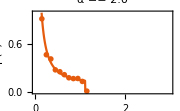

```mathematica
With[{g=1.75},With[{xLim=3,yLim=1,ticksSize=Medium,plotStyle=ColorData[108],label={ShiftFrameLabel[15]@"|z|",ShiftFrameLabel[-5]@"ρ(z)"},eigs=Eigenvalues@JacobianMatrix[2,g,Tanh,2000],DOSvector=JacobianDOSGaussianVector[g,Tanh],radius=JacobianGaussianRadius[g,Tanh]},Show[DOSvector//Append[{radius,0}]//ListLinePlot[#,PlotRange->{{0,xLim},{0,yLim}},ImageSize->Small,Frame->{True,True,False,False},FrameLabel->label,PlotLabel->StringTemplate["α == ``"]@2.0,Evaluate@FigureStyle@pubStyle[ticksSize],LabelStyle->pubStyle[],PlotStyle->plotStyle,ImagePadding->{{50,10},{50,10}}]&,{#1,#2/(2π#1)}&@@@(HistogramPDFList[#,{.1}]&)@Abs@eigs//ListPlot[#,PlotRange->{{0,xLim},{0,yLim}},PlotMarkers->{"OpenMarkers",Small},PlotStyle->plotStyle]/.{p:_Disk|_Polygon:>{FaceForm[],p}}&,Graphics@Inset[Show[ListPlot[ReIm@eigs,PlotRange->{{-xLim,xLim},{-xLim,xLim}},PlotMarkers->{"OpenMarkers",Tiny},AspectRatio->1,Evaluate@FigureStyle@pubStyle[ticksSize],PlotStyle->plotStyle,PlotRangeClipping->False,Ticks->{{3},{{3,3ⅈ}}}]/.{p:_Disk|_Polygon:>{FaceForm[],p}},Graphics@{Black,AbsoluteThickness[1.1],Circle[{0,0},DOSvector[[-1,1]]]}],Scaled@{1,1},Scaled@{1,1},Scaled@1],PlotRangeClipping->False]]]
```

```mathematica
Export["fig/spectrum_alpha_200.pdf",ResourceFunction["EvaluatePreviousCell"][]]
```

fig/spectrum_alpha_200.pdf

## Jacobian phase diagram

Compute the DOS vectors over a grid of alpha and g followed by the DOS vectors on the ordered transition line. These take a few hours of compute time over ~100 cores (note the BlockParallels for threading)

```mathematica
ParallelOuter[{α,g}↦Quiet@JacobianDOSVector[α,g,.01,Tanh,100000],Range[.5,1.9,.1],Range[1,3,.1]]//BinarySerialize
```

ByteArray[…]

```mathematica
BlockParallel[5,ResourceFunction["ParallelMapMonitored"][α↦With[{g=Quiet@JacobianOrderedTransition[α,0.01,Tanh]},{α,g,Quiet@JacobianDOSVector[α,g,.01,Tanh,100000]}],Range[.5,1.9,.1]]//BinarySerialize]
```

ByteArray[…]

```mathematica
ParallelOuter[{α,g}↦Quiet@JacobianDOSVector[α,g,.01,Tanh,100000],Range[1.9,1.99,.01],Range[1,2,.01]]//BinarySerialize
```

ByteArray[…]

```mathematica
BlockParallel[5,ResourceFunction["ParallelMapMonitored"][α↦With[{g=Quiet@JacobianOrderedTransition[α,0.01,Tanh]},{α,g,Quiet@JacobianDOSVector[α,g,.01,Tanh,100000]}],Range[1.9,1.99,.01]]//BinarySerialize]
```

ByteArray[…]

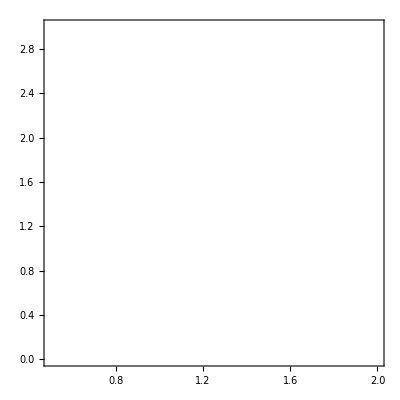

```mathematica
Show[Table[With[{colour=White,data=BinaryDeserialize@*ResourceFunction["EvaluatePreviousCell"]/@{pos+2,pos}},List[Table[With[{f=(#-1)^n&},With[{αg=Map[Total[#1f[#1]#2&@@@#]&,data[[1]],{2}],αTransition=data[[2]]//Map[MapAt[Total[#1f[#1]#2&@@@#]&,-1]]},ListContourPlot[Transpose@(αg/Last/@αTransition),DataRange->(pos/.{5->{{.5,1.9},{1,3}},1->{{1.9,1.99},{1,2}}}),PlotRange->{{.5,2},{0,3}},Contours->{1},ContourShading->None,ContourStyle->{Thick,Dashed,Opacity[n/9,colour]},ContourLabels->(If[1.5<#2<2,Text[Style[n,pubStyle[],colour,Opacity[n/9],Large],{#1,#2}]]&)]]],{n,1,9,2}],ListLinePlot[Most/@data[[2]],PlotStyle->{Thick,Dashed,colour}]]],{pos,{5,1}}]]
```

```mathematica
ResourceFunction["ParallelMapMonitored"][α↦{α,g/.With[{ϕ=Tanh},Quiet@FindRoot[g(Abs[s]/2)^(1/α)-.001/.FindRoot[Abs[s]-NExpectation[Abs[ϕ[h]]^α,h\[Distributed]StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)]],{s,1,.5}],{g,1,.5}]]},Range[.5,1.99,.01]]//BinarySerialize
```

ByteArray[…]

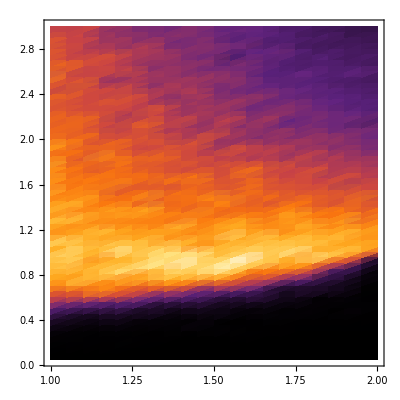
```mathematica
Show[-Graphics-,ResourceFunction["EvaluatePreviousCell"][3],BinaryDeserialize@ResourceFunction["EvaluatePreviousCell"][]//ListLinePlot[Select[#,GreaterThan[1]@*First],PlotStyle->{Red},PlotRange->{{1,2},{0,3}}]&,Graphics@{Green,PointSize[Large],Point[{{2,1.75},{1.2,1.75}}]},PlotRange->{{1,2},{0,3}},PlotRangeClipping->True(*,Background->Black*),FrameStyle->pubStyle[16],FrameLabel->{ShiftFrameLabel[15]@"α",ShiftFrameLabel[-5]@"g"}]
```